# MAT: 150 -- Lab 3

## Date: 9/22/2017 Due: 9/27/2017

## 2D Vector Graphics

Recall our modest spaceship from class, which we define in homogenous coordinates below.

```mathematica
T={{0,2,1},{0,0,3},{1,1,1}};
```

When displaying the spaceship, we will use the Graphics and Triangle command. The latter is expecting three points, which correspond to the three columns of T, but only including the first 2 rows. We can do this as follows (note the use of the help function, to simplify the Graphics command).

```mathematica
help[T_]:=Triangle[{T[[1;;2,1]],T[[1;;2,2]],T[[1;;2,3]]}];
```

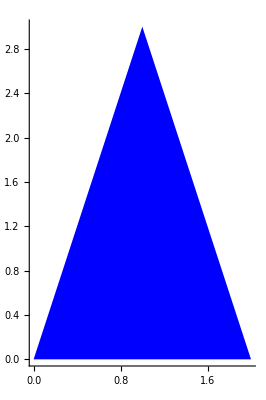

```mathematica
Graphics[{Blue,help[T]},Axes->True]
```

### Translation

To move our spaceship vertically and horizontally, we will make use of the fact that a translation can be represented as a linear transformation in the homogenous coordinate system.

```mathematica
trans[T_,r_,s_]:={{1,0,r},{0,1,s},{0,0,1}}.T;
```

We can get a sense for what these translations will look like using Manipulate (Animate but without the auto play). The blue triangle is the original, the red is the translated triangle.

```mathematica
Manipulate[Graphics[{Blue,help[T],Red, help[trans[T,r,s]]},Axes->True],{r,-2,2},{s,-2,2}]
```

### Rotation

In order to rotate our spaceship about its center (centroid), we need to compose a translation and its inverse with a rotation as follows.

```mathematica
mid[T_]:=RegionCentroid[help[T]];
```

The function mid uses RegionCentroid to compute the centroid of the Triangle represented by T, note that this function will work for more general regions as well.

```mathematica
rot[T_,t_]:=
Module[{r,s,Q},
r=mid[T][[1]];
s=mid[T][[2]];
Q={{Cos[t],-Sin[t],0},{Sin[t],Cos[t],0},{0,0,1}};
trans[Q.trans[T,-r,-s],r,s]]
```

Again, we will get a sense for this transformation using Manipulate.

```mathematica
Manipulate[Graphics[{Blue,help[T],Red,help[rot[T,t]]},Axes->True],{t,0,2*Pi}]
```

### Reflection

For our third move, we find it useful to be able to move back and forth from either side of the center vertical line. To this end, we introduce a reflection about the line L through the origin that makes a 90 degree angle, measured counterclockwise, with the x-axis.

```mathematica
ref[T_]:=
Module[{R},
R={{-1,0,0},{0,1,0},{0,0,1}};
R.T]
```

Below is a graphics that displays the original spaceship in blue, and the reflected spaceship in red.

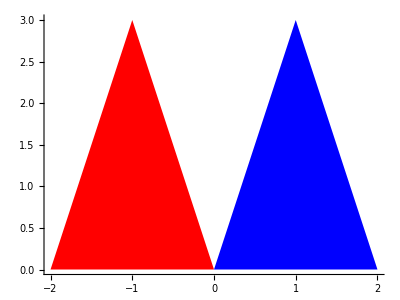

```mathematica
Graphics[{Blue,help[T],Red,help[ref[T]]},Axes->True]
```

### Put it all together in a GIF

At this point, we are ready to put all of our transformations together in one GIF. To this end, we will move our spaceship around using translations, rotations, and reflections. We compose these transformations one at a time, and in the process form a list of graphics. These lists are stored in the variable anim, and then exported to a gif file using the Export command.

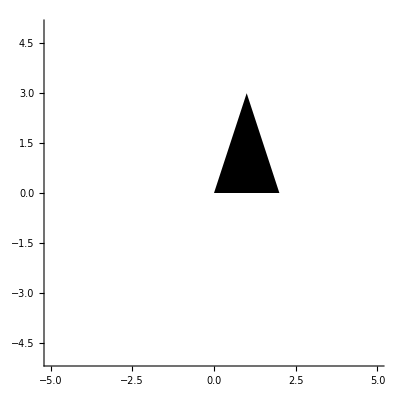
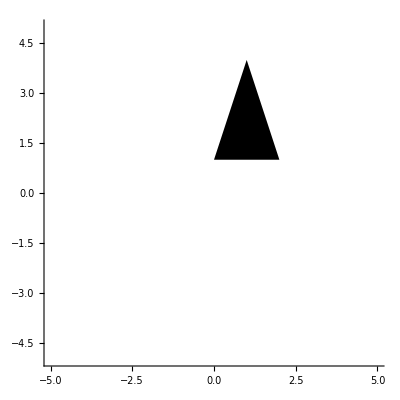
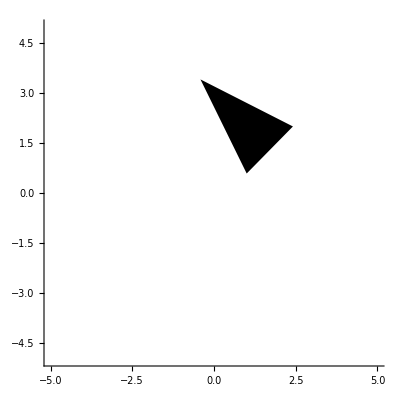
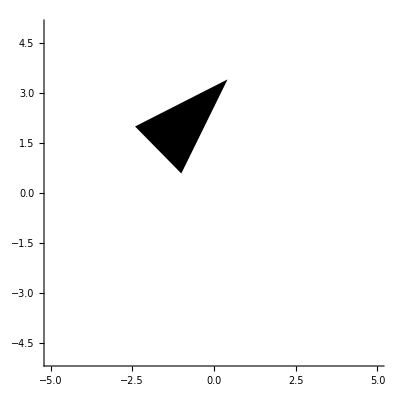
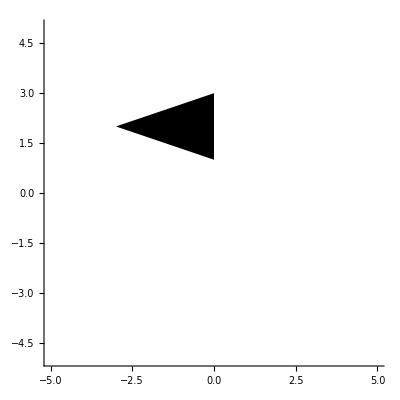
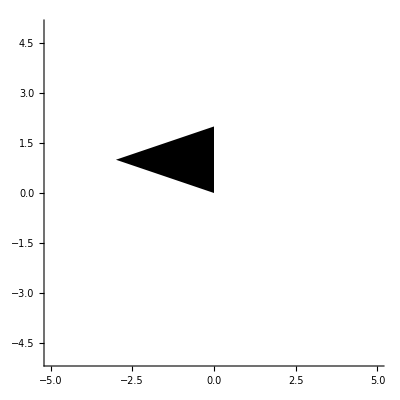
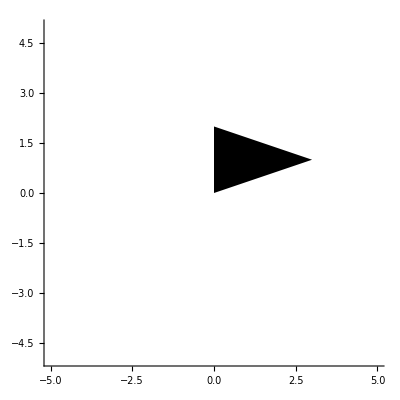
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
anim=List[Graphics[help[T],Axes->True,PlotRange->{{-5,5},{-5,5}}],Graphics[help[trans[T,0,1]],Axes->True,PlotRange->{{-5,5},{-5,5}}],Graphics[help[rot[trans[T,0,1],Pi/4]],Axes->True,PlotRange->{{-5,5},{-5,5}}],Graphics[help[ref[rot[trans[T,0,1],Pi/4]]],Axes->True,PlotRange->{{-5,5},{-5,5}}],Graphics[help[rot[ref[rot[trans[T,0,1],Pi/4]],3*Pi/4]],Axes->True,PlotRange->{{-5,5},{-5,5}}],Graphics[help[trans[rot[ref[rot[trans[T,0,1],Pi/4]],3*Pi/4],0,-1]],Axes->True,PlotRange->{{-5,5},{-5,5}}],Graphics[help[ref[trans[rot[ref[rot[trans[T,0,1],Pi/4]],3*Pi/4],0,-1]]],Axes->True,PlotRange->{{-5,5},{-5,5}}],Graphics[help[rot[ref[trans[rot[ref[rot[trans[T,0,1],Pi/4]],3*Pi/4],0,-1]],Pi/2]],Axes->True,PlotRange->{{-5,5},{-5,5}}]]
Export["~/anim.gif",anim];
```

## Assignment

Now, it is your turn.

Store your object as a matrix and define a helper function to help display that object as a Mathematica shape (Triangle, Parallelogram, etc).

Define whatever functions you need to perform the three transformations you selected on your object. Be specific about what transformations you choose and what functions you need, adding comments as necessary. In addition, show that each function works by providing an animation (or manipulate), as was done above.

Create a list of graphics that move your object from one place in the Cartesian plane to another, in an interesting fashion. Then, export this list of graphics as a gif.

Play the gif file in your browser and show off to your friends and family.